## GibbotQnts Package

```mathematica
BeginPackage["GibbotQnts`"];

If[Not@ValueQ[DynamicQnts::usage], DynamicQnts::usage = "Based on which magnet is on, state of the robot, and input torque, this function outputs the robot's acceleration and tangential forces felt by magnets on each link."];

If[Not@ValueQ[ImpactQnts::usage], ImpactQnts::usage = "Based on which magnet is on and the state of the robot, this function outputs the robot's post-impact velocity and tangential impulsive forces felt by magnets on each link."];

If[Not@ValueQ[MotorInput::usage], MotorInput::usage = "Returns input torque u such that b.qdd == 0.  b can be a vector or a matrix.  This function is useful if computing a (partial) feedback linearization term."];

If[Not@ValueQ[FreeFlightVelocity::usage], FreeFlightVelocity::usage = "Returns velocity of robot at the beginning of free flight required to travel a horizontal distance Δx at a maximum height of Δy given configuration q."];

If[Not@ValueQ[MinimizeFreeFlight::usage], MinimizeFreeFlight::usage = "Returns state that minimumizes velocity satisfying free flight required to travel a horizontal distance Δx at a maximum height of Δy."];

If[Not@ValueQ[MaximizeFreeFlight::usage], MaximizeFreeFlight::usage = "Returns state that maximumizes velocity satisfying free flight required to travel a horizontal distance Δx at a maximum height of Δy."];

If[Not@ValueQ[PE::usage], PE::usage = "Potential Energy."];
If[Not@ValueQ[KE::usage], KE::usage = "Kinetic Energy."];
If[Not@ValueQ[TE::usage], TE::usage = "Total Energy."];

If[Not@ValueQ[DrawGibbot::usage], DrawGibbot::usage = "Draws the Gibbot."];

If[Not@ValueQ[g::usage], g::usage = "gravity"];
If[Not@ValueQ[m1::usage], m1::usage = "mass of link 1"];
If[Not@ValueQ[m2::usage], m2::usage = "mass of link 2"];
If[Not@ValueQ[I1::usage], I1::usage = "moment of inertia about com of link 1"];
If[Not@ValueQ[I2::usage], I2::usage = "moment of inertia about com of link 2"];
If[Not@ValueQ[r1::usage], r1::usage = "position of com of link 1"];
If[Not@ValueQ[r2::usage], r2::usage = "position of com of link 2"];
If[Not@ValueQ[L1::usage], L1::usage = "length of link 1"];
If[Not@ValueQ[L2::usage], L2::usage = "length of link 2"];
If[Not@ValueQ[T::usage], T::usage = "mapping from motor torque to generalized forces"];

Begin["`Private`"];

(* default parameter values *)
g = 9.81; (* gravity *)
m1 = m2 = 0.453592 4; (* lbs to kg *)
I1 = I2 = 0.04185679;
L1 = L2 = 0.0254 11; (* inches to m *)
r1 = (1-0.7)L1; (* center of mass *)
r2 = 0.7L2; (* center of mass *)
b1 = 0.0; (* bearing friction *)
b2 = 0.5; (* motor friction *)
T = {0, 0, 0, 1} ; (* transmission matrix from motor to robot *)
(*Protect[g, m1, I1, I2, L1, L2, r1, r2, T];*)

M[q_] := Module[{c3,s3,c4, c34, s34, A, B, C},
c3 = Cos[q⟦3⟧];
s3 = Sin[q⟦3⟧];
c4 = Cos[q⟦4⟧];
c34 = Cos[q⟦3⟧+q⟦4⟧];
s34 = Sin[q⟦3⟧+q⟦4⟧];
A = ({{m1+m2, 0}, {0, m1+m2}});
B = ({{c3 (L1 m2+m1 r1)+c34 m2 r2, c34 m2 r2}, {(L1 m2+m1 r1) s3+m2 r2 s34, m2 r2 s34}});
C = ({{I1+I2+L1^2 m2+m1 r1^2+2 c4 L1 m2 r2+m2 r2^2, I2+c4 L1 m2 r2+m2 r2^2}, {I2+c4 L1 m2 r2+m2 r2^2, I2+m2 r2^2}});

ArrayFlatten[{{A, B}, {Bᵀ, C}}]
];

c[x_] := Module[{c3,s3,s4, c34, s34},
c3 = Cos[x⟦3⟧];
s3 = Sin[x⟦3⟧];
s4 = Sin[x⟦4⟧];
c34 = Cos[x⟦3⟧+x⟦4⟧];
s34 = Sin[x⟦3⟧+x⟦4⟧];

({{1/2 (-2 m1 r1 s3 x⟦7⟧^2+2 m2 (-L1 s3 x⟦7⟧^2-r2 s34 (x⟦7⟧+x⟦8⟧)^2))}, {g (m1+m2)+1/2 (2 m1 r1 c3 x⟦7⟧^2+2 m2 (L1 c3 x⟦7⟧^2+r2 c34 (x⟦7⟧+x⟦8⟧)^2))}, {g (L1 m2 s3+m1 r1 s3+m2 r2 s34)-2 L1 m2 r2 s4 x⟦7⟧ x⟦8⟧-L1 m2 r2 s4 x⟦8⟧^2}, {m2 r2 (g s34+L1 s4 x⟦7⟧^2)}})
];

fext[x_, u_] := T u - T b2 x⟦8⟧;

J1[x_] := {({{1, 0, 0, 0}, {0, 1, 0, 0}}), ({{0, 0, 0, 0}, {0, 0, 0, 0}})};

J2[x_] := Module[{c3,s3, c34, s34, J, Jdot},
c3 = Cos[x⟦3⟧];
s3 = Sin[x⟦3⟧];
c34 = Cos[x⟦3⟧+x⟦4⟧];
s34 = Sin[x⟦3⟧+x⟦4⟧];

J = ({{1, 0, L1 c3+L2 c34, L2 c34}, {0, 1, L1 s3+L2 s34, L2 s34}});
Jdot = ({{0, 0, -L1 s3 x⟦7⟧-L2 s34 (x⟦7⟧+x⟦8⟧), -L2 s34 (x⟦7⟧+x⟦8⟧)}, {0, 0, L1 c3 x⟦7⟧+L2 c34 (x⟦7⟧+x⟦8⟧), L2 c34 (x⟦7⟧+x⟦8⟧)}});

{J, Jdot}
];

J3[x_] := Module[{c3,s3, c34, s34, J, Jdot},
c3 = Cos[x⟦3⟧];
s3 = Sin[x⟦3⟧];
c34 = Cos[x⟦3⟧+x⟦4⟧];
s34 = Sin[x⟦3⟧+x⟦4⟧];
J = ({{1, 0, 0, 0}, {0, 1, 0, 0}, {1, 0, L1 c3+L2 c34, L2 c34}, {0, 1, L1 s3+L2 s34, L2 s34}});
Jdot = ({{0, 0, 0, 0}, {0, 0, 0, 0}, {0, 0, -L1 s3 x⟦7⟧-L2 s34 (x⟦7⟧+x⟦8⟧), -L2 s34 (x⟦7⟧+x⟦8⟧)}, {0, 0, L1 c3 x⟦7⟧+L2 c34 (x⟦7⟧+x⟦8⟧), L2 c34 (x⟦7⟧+x⟦8⟧)}});

{J, Jdot}
];

dPcom[mag_, q_] := Module[{m, c3,s3, c34, s34},
(* dPcom = d/dq Pcom, where Pcom is the center of mass of the robot. *)
(* This function satisfies vcom = dPcom.qd⟦3;;4⟧, where vcom is the *)
(* velocity of the center of mass when the robot has only one magnet *)
(* on and qd = d/dt {qx, qy ,qθ1, qθ2}. *)
m = m1 + m2; (* total mass *)
c3 = Cos[q⟦3⟧];
s3 = Sin[q⟦3⟧];
c34 = Cos[q⟦3⟧+q⟦4⟧];
s34 = Sin[q⟦3⟧+q⟦4⟧];
(1/m) Which[
mag == 0, ({{m1+m2, 0, (L1 m2+m1 r1) c3+m2 r2 c34, m2 r2 c34}, {0, m1+m2, (L1 m2+m1 r1) s3+m2 r2 s34, m2 r2 s34}}),
mag == 1, ({{(L1 m2+m1 r1) c3+m2 r2 c34, m2 r2 c34}, {(L1 m2+m1 r1) s3+m2 r2 s34, m2 r2 s34}}),
mag == 2, ({{-m1 (L1-r1) c3+(L2 (m1+m2)-m2 r2) c34, -(L2 (m1+m2)-m2 r2) c34}, {-m1 (L1-r1) s3+(L2 (m1+m2)-m2 r2) s34, -(L2 (m1+m2)-m2 r2) s34}}),
True, Throw["Invalid magnet state for dPcom"]
]
];

(* position of center of masses and end points on each link *)
P0[q_] := q⟦1;;2⟧;
P1[q_] := P0[q] + r1{Sin[q⟦3⟧], -Cos[q⟦3⟧]};
P2[q_] := P3[q] + r2{Sin[q⟦3⟧+q⟦4⟧], -Cos[q⟦3⟧+q⟦4⟧]};
P3[q_] := P0[q] + L1{Sin[q⟦3⟧], -Cos[q⟦3⟧]};
P4[q_] := P3[q] + L2{Sin[q⟦3⟧+q⟦4⟧], -Cos[q⟦3⟧+q⟦4⟧]};

(* energy *)
KE[x_] := 1/2x⟦5;;8⟧.M[x].x⟦5;;8⟧;
PE[q_] := g (m1 P1[q]+m2 P2[q]).{0,1};
TE[x_] := KE[x] + PE[x];

DynamicQnts[mag_, x_, u_] := Module[{q, qd, qdd, λ, J, Jd, Minv, Λ},
Which[
mag == 0, J = {}, (* both magnets off *)
mag == 1, {J, Jd} = J1[x], (* magnet on link 1 on *)
mag == 2, {J, Jd} = J2[x], (* magnet on link 2 on *)
mag == 3, {J, Jd} = J3[x], (* both magnets on *)
True, Throw["Invalid Magnet State for DynamicQnts"]
];

q = x⟦1;;4⟧; (* configuration *)
qd = x⟦5;;8⟧; (* velocity *)
Minv = Inverse[M[q]];

λ = {0,0,0,0}; (* forces on magnets *)
qdd = Minv.(fext[x, u] - c[x]); (* acceleration *)

If[J ≠ {}, 
Λ = Inverse[J.Minv.Jᵀ];
λ = -Λ.(Jd.qd + J.qdd);
qdd = qdd + Minv.Jᵀ.λ;

λ = If[mag == 1, PadRight[λ, 4], PadLeft[λ, 4]];
];

{qdd, λ}
];

ImpactQnts[mag_, x_] := Module[{q, qd, J, Minv, v, λ, Λ},
Which[
mag == 0, J = {}, (* both magnets off *)
mag == 1, J = First@J1[x], (* magnet on link 1 on *)
mag == 2, J = First@J2[x], (* magnet on link 2 on *)
mag == 3, J = First@J3[x], (* both magnets on *)
True, Throw["Invalid Magnet State for DynamicQnts"]
];

q = x⟦1;;4⟧; (* configuration *)
qd = x⟦5;;8⟧; (* pre-impact velocity *)
Minv = Inverse[M[q]];

λ = {0,0,0,0}; (* impulsive force on magnets *)
v = qd; (* post-impact velocity *)

If[J ≠ {}, 
Λ = Inverse[J.Minv.Jᵀ];
λ = -Λ.J.v;
v = v + Minv.Jᵀ.λ;

λ = If[mag == 1, PadRight[λ, 4], PadLeft[λ, 4]];
];

{v, λ}
];

MotorInput[mag_, x_, b_, v_:0] := Module[{q, qd, J, Jd, Minv, zi, zs, Λ},
(* returns input torque u such that b.qdd == du, where *)
(* qdd = d^2/dt^2 {qx, qy ,qθ1, qθ2}. This can be used to apply feedback *)
(* linearization when using the optional parameter du. *)
Which[
mag == 0, J = {}, (* both magnets off *)
mag == 1, {J, Jd} = J1[x], (* magnet on link 1 on *)
mag == 2, {J, Jd} = J2[x], (* magnet on link 2 on *)
mag == 3, {J, Jd} = J3[x], (* both magnets on *)
True, Throw["Invalid Magnet State for MotorInput"]
];

q = x⟦1;;4⟧; (* configuration *)
qd = x⟦5;;8⟧; (* velocity *)
Minv = Inverse[M[q]];

zi = Minv.(fext[x, 0] - c[x]); (* zero-input acceleration *)
zs = Minv.T; (* zero-state acceleration *)

If[J ≠ {}, 
(*
Λ = Inverse[J.Minv.Jᵀ];
zi = zi - Minv.Jᵀ.Λ.(Jd.qd + J.zi);
zs = zs - Minv.Jᵀ.Λ.J.zs;
*)
Λ = Minv.Jᵀ.Inverse[J.Minv.Jᵀ];
zi = zi - Λ.(Jd.qd + J.zi);
Λ = Λ.J;
zs = zs - Λ.zs;
];

(* cancel out dynamics and add controller v *)
-b.zi/b.zs + v/If[MatrixQ[b], Norm[# zs]&/@ b, Norm[b zs]]
];

FreeFlightVelocity[mag_, q_, Δx_, Δy_] := Module[{vcom, θd, qd, dP, dq, c3, s3, c34, s34},
(* solve θd such that vcom = dP.θd, where θd = d/dt{θ1, θ2}, *)
(* dP = d/dq Pcom, where Pcom is the center of mass of the robot, *)
(* and vcom is the velocity of the center of mass. *)
(* unique solutions do not exist whenever q⟦4⟧ == 0 mod π *)
(* if q⟦4⟧ == 0, then a line of slns exist Δy = Tan[q⟦3⟧]/2 Δx. *)
dP = dPcom[mag, q];
vcom = {g Δx/Sqrt[2 g Δy], Sqrt[2 g Δy]};
θd = LinearSolve[dP, vcom];

(* return qd = d/dt {qx, qy, qθ1, qθ2} subject to a magnet being on *)
c3 = Cos[q⟦3⟧];
s3 = Sin[q⟦3⟧];
c34 = Cos[q⟦3⟧+q⟦4⟧];
s34 = Sin[q⟦3⟧+q⟦4⟧];

(* dPcom already does a sanity check on magnet values *)
dq = If[mag == 1, ({{0, 0}, {0, 0}, {1, 0}, {0, 1}}), ({{-L1 c3-L2 c34, -L2 c34}, {-L1 s3-L2 s34, -L2 s34}, {1, 0}, {0, 1}})];
dq.θd
];

MinimizeFreeFlight[mag_, Δx_, Δy_] := Module[{q, qx,qy, qθ1, qθ2, θ, θd},
(* solve θ such that 1/2 θd.θd is minimized, where θd is the initial *)
(* velocity during free flight required to travel a distance of Δx at *)
(* a maximum height Δy, and θ = {qθ1, qθ2} for when the robot has only *)
(* one magnet on (a "pinned" configuration). *)

Which[
mag == 1, {qx, qy} = {0, 0},
mag == 2, {qx, qy} = {-L1 Sin[qθ1]-L2 Sin[qθ1+qθ2], L1 Cos[qθ1]+L2 Cos[qθ1+qθ2]},
True, Throw["Invalid magnet state for MinimizeFreeFlight"]
];

q = {qx,qy, qθ1, qθ2}; (* configuration *)
θd = FreeFlightVelocity[mag, q, Δx, Δy]⟦3;;4⟧ // Simplify;
{qθ1, qθ2} = ArgMin[1/2θd.θd, {qθ1, qθ2}];

Join[q, FreeFlightVelocity[mag, q, Δx, Δy]]
];

MaximizeFreeFlight[mag_, Δx_, Δy_, α_:1] := Module[{q, qx,qy, qθ1, qθ2, θ, θd},
(* solve θ such that 1/2 θd.θd is maximized subject to θd⟦3⟧ = α θd⟦4⟧, *)
(* where θd is the initial velocity during free flight required to travel *)
(* a distance of Δx at a maximum height Δy, and θ = {qθ1, qθ2} for when the *) (* robot has only one magnet on (a "pinned" configuration). *)

Which[
mag == 1, {qx, qy} = {0, 0},
mag == 2, {qx, qy} = {-L1 Sin[qθ1]-L2 Sin[qθ1+qθ2], L1 Cos[qθ1]+L2 Cos[qθ1+qθ2]},
True, Throw["Invalid magnet state for MaximizeFreeFlight"]
];

q = {qx,qy, qθ1, qθ2}; (* configuration *)
θd = FreeFlightVelocity[mag, q, Δx, Δy]⟦3;;4⟧ // Simplify;
{qθ1, qθ2} = ArgMax[{1/2θd.θd, θd⟦1⟧ == α θd⟦2⟧}, {qθ1, qθ2}];

(* visualize cost function, useful for debugging *)
(*
ParametricPlot[θd, {qθ1, -π,π}, {qθ2, -π,π}, Epilog-> InfiniteLine[{{0,0}, {α,1}}]]
*)
Join[q, FreeFlightVelocity[mag, q, Δx, Δy]]
];

DrawGibbot[mag_, x_, opts:OptionsPattern[Graphics]] := Module[{P, psz, ma, com, mo, li},
psz = 0.01 Max[L1, L2]/0.3;
(* get positions *)
P = {x⟦1;;2⟧, P1[x], P2[x], P3[x], P4[x]};
(* motor *)
mo = {Red, Disk[P⟦4⟧, 2psz]};
(* center of mass of each link *)
com = {Gray, Disk[P⟦2⟧, psz], Disk[P⟦3⟧, psz]};
(* magnets: on -> dark, off -> light *)
ma = Which[
mag == 0, {LightRed, LightRed}, 
mag == 1, {Red, LightRed},
mag == 2, {LightRed, Red},
mag == 3, {Red, Red}
];
ma = {ma⟦1⟧, Disk[P⟦1⟧, psz], ma⟦2⟧, Disk[P⟦5⟧, psz]};
(* links *)
li = {Thick, Black, Line[{P⟦{1,4,5}⟧}]};
Graphics[{li, mo, ma, com}, opts]
];

SetAttributes[FixAngles, Listable];
FixAngles[q_] := Module[{x}, 
(* make sure angles are btw (-pi pi] *)
x = Mod[q, 2π];
If[x>π, x - 2π, x]
];

FixState[x_] := Module[{y = x, n}, 
n = 4;
If[ListQ[y⟦1⟧],
y⟦All,3;;4⟧ = FixAngles[y⟦All, 3;;4⟧], 
y⟦3;;4⟧ = FixAngles[y⟦3;;4⟧]];
y
];

End[];
EndPackage[];
```

g::shdw: Symbol "g" appears in multiple contexts {"GibbotQnts`", "Global`"}; definitions in context "GibbotQnts`" may shadow or be shadowed by other definitions.

## Examples

```mathematica
(* robot configuration: q = {qx, qy, qθ1, qθ2} *)
mag = RandomInteger[{0,3}] (* magnet state: 0 = both off...3 = both on *)
x = RandomReal[{-1,1}, 8] (* robot state: {q, dq/dt} *)
u = RandomReal[{-1,1}] (* motor output *)
dx = 2L1; (* free flight distance @ maximum height *)
dy = L1; (* maximum height during free flight *)

(* errors and bizarre answers may result if constraint Jmag[q].dq/dt isn't satisfied *)

(* dynamics and impacts *)
DynamicQnts[mag, x, u] (* returns accelerations and tangential loads on each magnet *)
ImpactQnts[mag, x] (* returns post-impact state and impulse felt by each magnet *)

(* input torque from motor *)
b = {0,0,0,1}; (* vector for finding a u such that b.qdd = 0 *)
u = MotorInput[mag, x, b] (* input torque needed to make d^2/dt^2 qθ2 = 0 *)
DynamicQnts[mag, x, u]⟦1⟧ // Chop

(* double pendulum to free flight *)
If[ 0 < mag < 3, 
FreeFlightVelocity[mag, x, dx, dy] (* returns velocity required to travel (dx, dy) *)
]

If[ 0 < mag < 3, 
MinimizeFreeFlight[mag, dx, dy] (* returns state that minimizes velocity required *)
]

If[ 0 < mag < 3, 
MaximizeFreeFlight[mag, dx, dy, 1/2] (* returns state that maximizes velocity subject to d/dt q3 == 1/2 d/dt q4 *)
] 

DrawGibbot[mag, x] (* returns a graphic of the gibbot *)
```

## Specs

```mathematica
f[s_?NumericQ, q_, qd_] := Module[{x}, x = Join[q,qd]; First@DynamicQnts[mag, x, u[s, x]]];
```

```mathematica
V[x_] := Module[{E, Emax},
Emax = TE[Join[x⟦1;;2⟧, {π, 0}, ConstantArray[0, 4]]];
E = TE[x] - Emax;
1/2(ke E^2 + kp x⟦4⟧^2 + kd x⟦8⟧^2)
];

Vdot[x_, u_] := Module[{E, Emax, qdd},
qdd = First@DynamicQnts[mag, x, u];
Emax = TE[Join[x⟦1;;2⟧, {π, 0}, ConstantArray[0, 4]]];
E = TE[x] - Emax;
(ke E u + kd qdd⟦4⟧ + kp x⟦4⟧)x⟦8⟧
];

zizs[x_] := Module[{f, J, Jd, Minv, zi, zs, Λ},
Which[
mag == 1, {J, Jd} = GibbotQnts`Private`J1[x], (* magnet on link 1 on *)
mag == 2, {J, Jd} = GibbotQnts`Private`J2[x], (* magnet on link 2 on *)
True, Throw["Invalid Magnet State for zizs"]
];

Minv = Inverse[GibbotQnts`Private`M[x⟦1;;4⟧]];
f = GibbotQnts`Private`fext[x, 0] - GibbotQnts`Private`c[x];

zi = Minv.f; (* zero-input acceleration *)
zs = Minv.T; (* zero-state acceleration *)
Λ = Minv.Jᵀ.Inverse[J.Minv.Jᵀ];
zi = zi - Λ.(Jd.x⟦5;;8⟧ + J.zi);
Λ = Λ.J;
zs = zs - Λ.zs;

{zi, zs}
];

gains[] := Module[{zsmin, x3, x4, c4, c5},
c4 = zizs[{0,0,x3,x4,0,0,0,0}]⟦2, 4⟧;
c5 = RegionProduct[Line[{{0},{2π}}],Line[{{0},{2π}}]];
zsmin = NMinValue[c4, {x3,x4} ∈ c5];

c4 = m1 r1 + m2 L1;
c5 = m2 r2;
(* {kd/ke, kp/ke} ≥  *)
{2(c4+c5)g/zsmin, 2 c4 c5 g^2}
];

u[t_, x_] := Module[{E, Emax, zi, zs},
{zi, zs} = zizs[x];
Emax = TE[Join[x⟦1;;2⟧, {π, 0}, ConstantArray[0, 4]]];
E = TE[x] - Emax;
If[t < tsw, 
(-kv x⟦8⟧ - kp x⟦4⟧ - kd zi⟦4⟧)/(ke E + kd zs⟦4⟧),
0(*-K.(x⟦{3,4,7,8}⟧ - {π,0,0,0})*)
]
];
```

```mathematica
mag = 1;
kv = 30;
ke = 10;
{kd, kp} = {1, 1} gains[] ke
```

{21.8645,450.104}

```mathematica
mag = 1;
t = 25;
x = ConstantArray[0, 8];
x⟦8⟧ = -1;
x⟦3⟧ = 30 Degree;
x⟦4⟧ = 0 Degree;

Clear[q];
tsw = ∞;
q = q/.First@NDSolve[
{
q''[s] == f[s, q[s], q'[s]], 
q[0] == x⟦1;;4⟧, 
q'[0] == x⟦5;;8⟧,
WhenEvent[{0,0,0,1}.q[s]-π, "StopIntegration"],
WhenEvent[{0,0,0,1}.q[s]+π, "StopIntegration"],
WhenEvent[{0,0,1,0}.q[s]-π, tsw = s;"StopIntegration"],
WhenEvent[{0,0,1,0}.q[s]+π ==   0, tsw = s;"StopIntegration"],
WhenEvent[{0,1}.GibbotQnts`Private`P4[q[s]], ty = s;]
}, 
q, {s, 0, t},
MaxStepSize->0.01
];

tsw
t = q["Domain"]⟦1,2⟧;
q'[t]
Animate[DrawGibbot[mag, q[s], PlotRange-> 1.5(L1+L2)], {s, 0, t}, AnimationRepetitions->1];
```

1.53624

{-6.26131×10^-16,5.26495×10^-16,5.52966,-7.52847}

```mathematica
Plot[{q[s]⟦3⟧-π, q'[s]⟦3⟧}, {s, 0, t}, PlotRange->All, Epilog->{Line[{{0, π}, {t, π}}], Line[{{0, -π}, {t, -π}}]}]
Plot[(TE[Join[q[s], q'[s]]]-TE[Join[x⟦1;;2⟧, {π, 0}, ConstantArray[0, 4]]])/TE[Join[x⟦1;;2⟧, {π, 0}, ConstantArray[0, 4]]], {s, 0, t}];
ParametricPlot[{{0,0,1,0}.q[s], {0,0,1,0}.q'[s]}, {s, 0, t}];
Plot[u[s, Join[q[s], q'[s]]], {s, 0, t}, PlotRange->All]
Plot[{0,0,0,60/2/π}.q'[s], {s, 0, t}, PlotRange->All]
RootMeanSquare[Table[u[s, Join[q[s], q'[s]]], {s,0,t, t/200}]]
RootMeanSquare[Table[{0,0,0,60/2/π}.q'[s], {s,0,t, t/200}]]
```

```mathematica
N2lbf = 1/4.4482216;
Plot[N2lbf Rest@DynamicQnts[mag, Join[q[s], q'[s]], u[s, Join[q[s], q'[s]]]], {s, 0, t}, PlotRange->All]

N2lbf Max[Table[Max@Rest@DynamicQnts[mag, Join[q[s], q'[s]], u[s, Join[q[s], q'[s]]]], {s,0,t, t/200}]]
```

```mathematica
Quiet@ParametricPlot[{u[s, Join[q[s], q'[s]]], {0,0,0,60/2/π}.q'[s]}, {s, 0, t}, AspectRatio-> 1]
```

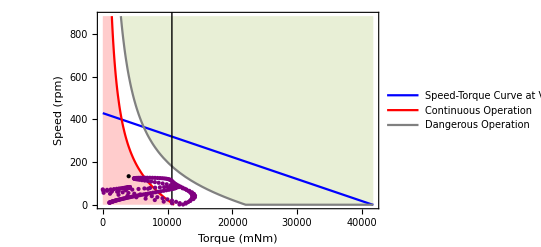

```mathematica
SpeedTorqueCurve[10, 25, Point@Table[Abs@{u[s, Join[q[s], q'[s]]] 1000, q'[s]⟦4⟧ 60/2/π}, {s,0,t, t/200}]]
```

```mathematica
Pcom[q_] := (m1 GibbotQnts`Private`P1[q] + m2 GibbotQnts`Private`P2[q])/(m1+m2);
Vcom[q_, qd_] := GibbotQnts`Private`dPcom[mag, q].qd;
```

```mathematica
dx = 2L1;
dy = L1;
mag = 1;
x = MinimizeFreeFlight[mag, dx, dy]
u = 0&;
m2 g r2;

Clear[q];
mag = 0;
t = 2Sqrt[2g dy]/g;
q = q/.First@NDSolve[
{
q''[s] == f[s, q[s], q'[s]], 
q[0] == x⟦1;;4⟧, 
q'[0] == x⟦5;;8⟧
}, 
q, {s, 0, t}
];

t = q["Domain"]⟦1,2⟧;

Animate[
Show[DrawGibbot[mag, q[s], PlotRange-> {{-(L1+L2)/2, 3dx}, {-(L1+L2), 2dy}}, Epilog-> {PointSize[Large], Point[{dx, dy}+Pcom[q[0]]], Blue, Point[Pcom[q[s]]]}], If[s > 0, (* ParametricPlot is a whiny little function *)Quiet@ParametricPlot[Pcom[q[a]], {a, 0, s}], Graphics[{}]]], {s, 0, t}, AnimationRepetitions->1]
```

```mathematica
Max@Flatten@Table[Max@Abs@DynamicQnts[1, Join[{0,0,th1, th2}, x⟦5;;8⟧], 0 u[0, x]], {th1, -π, π, 1/100}, {th2, -π, π, 1/100}]
```

```mathematica
374 N2lbf
```

```mathematica
q[0]
q'[0]
Pcom[q[0]]
Vcom[q[0], q'[0]]
```

```mathematica
ImpactQnts[1, Join[q[t], q'[t]]] // Chop
ImpactQnts[2, Join[q[t], q'[t]]] // Chop

ImpactQnts[1, Join[q[t/2], q'[t/2]]] // Chop
ImpactQnts[2, Join[q[t/2], q'[t/2]]] // Chop
```

```mathematica
TE@x
```

```mathematica
m2 r2 g
```

## Specs-old

```mathematica
mag = 1;
dx = 2L1;
dy = L1;
x = MinimizeFreeFlight[mag, dx, dy] // Chop;
m2 g r2;

K = Flatten@Module[{θ, x, x1,x2,x3,x4,x5,x6,x7,x8, u, rep, A, B},
x = {0,0,x3,x4,0,0,x7,x8};
x⟦5;;6⟧ = -GibbotQnts`Private`J1[x]⟦1⟧.x⟦5;;8⟧;
x⟦1;;2⟧ = -GibbotQnts`Private`P3[x];
rep = {x3-> π, x4-> π, x7-> 0, x8-> 0, u-> 0};
θ = x⟦{3,4,7,8}⟧;

x = Join[x⟦5;;8⟧, First@DynamicQnts[mag, x, u]];
A = D[x, {θ}]/. rep // Simplify // Chop;
B = D[x, {u}]/. rep // Simplify // Chop;

x = StateSpaceModel[{A⟦{3,4,7,8}⟧, {B⟦{3,4,7,8}⟧}ᵀ, ConstantArray[0, {1,4}]}];
LQRegulatorGains[x, {IdentityMatrix[4], IdentityMatrix[1]}]
];

pump = True;
b = {0,0,0,1};
v[x_, kp_, kd_] := kp(72Degree  ArcTan[x⟦7⟧] - x⟦4⟧) - kd x⟦8⟧;
(*v[x_, kp_, kd_] := (kp(π/2-x⟦3⟧)) + kd (0-x⟦7⟧);*)
u[t_, x_, kp_:0, kd_:0] := If[pump == True, MotorInput[mag, x, b, v[x, kp, kd]], -K.(x⟦{3,4,7,8}⟧ - {π,0,0,0})];

(* verify that the sign is correct for v, it should be positive *)
(* Chop@Simplify@First@DynamicQnts[mag, x, MotorInput[mag, x, b, v]] *)

x = ConstantArray[0, 8];

pump = False;
x⟦8⟧ = -1/10;
x⟦3⟧ = 0π;
x⟦4⟧ = 0π;

x⟦5;;6⟧ = -GibbotQnts`Private`J1[x]⟦1, All, 3⟧ x⟦7⟧;
(* ensure that constraints are satisfied *)
Norm[GibbotQnts`Private`J1[x]⟦1⟧.x⟦5;;8⟧] ==  0

t = 2;
kp = 0;
kd = 0;

f[s_?NumericQ, q_, qd_] := Module[{x}, x = Join[q,qd]; First@DynamicQnts[mag, x, u[s, x, kp, kd]]];
Clear[q];
tsw = ∞;
catch = π;
q = q/.First@NDSolve[{q''[s] == f[s, q[s], q'[s]], q[0] == x⟦1;;4⟧, q'[0] == x⟦5;;8⟧, WhenEvent[{0,0,0,1}.q[s]-π == 0, "StopIntegration"], WhenEvent[{0,0,0,1}.q[s]+π == 0, "StopIntegration"], 
WhenEvent[{0,0,1,0}.q[s]-catch ==   0, tsw = s;pump = False; "RemoveEvent"],
WhenEvent[{0,0,1,0}.q[s]+catch ==   0, tsw = s;pump = False; "RemoveEvent"]
}, 
q, {s, 0, t}];

tsw
t = q["Domain"]⟦1,2⟧;
Animate[DrawGibbot[mag, q[s], PlotRange-> 2.5L1], {s, 0, t}, AnimationRepetitions->1]
```

```mathematica
K = Flatten@Module[{θ, x, x1,x2,x3,x4,x5,x6,x7,x8, u, rep},
x = {0,0,x3,x4,0,0,x7,x8};
x⟦5;;6⟧ = -GibbotQnts`Private`J1[x]⟦1⟧.x⟦5;;8⟧;
x⟦1;;2⟧ = -GibbotQnts`Private`P3[x];
rep = {x3-> π, x4-> π, x7-> 0, x8-> 0, u-> 0};
θ = x⟦{3,4,7,8}⟧;

x = Join[x⟦5;;8⟧, First@DynamicQnts[mag, x, u]];
A = D[x, {θ}]/. rep // Simplify // Chop;
B = D[x, {u}]/. rep // Simplify // Chop;

x = StateSpaceModel[{A⟦{3,4,7,8}⟧, {B⟦{3,4,7,8}⟧}ᵀ, ConstantArray[0, {1,4}]}];
LQRegulatorGains[x, {IdentityMatrix[4], IdentityMatrix[1]}]
];

u[t_, x_, kp_:0, kd_:0] := -K.(x⟦{3,4,7,8}⟧ - {π,π,0,0});

x = ConstantArray[0, 8];
x⟦7⟧ = 0;
x⟦3⟧ = π - π/10;
x⟦4⟧ = π;
x⟦5;;6⟧ = -GibbotQnts`Private`J1[x]⟦1, All, 3⟧ x⟦7⟧;

t = 5;

Check[
Clear[q];
q = q/.First@NDSolve[{q''[s] == f[s, q[s], q'[s]], q[0] == x⟦1;;4⟧, q'[0] == x⟦5;;8⟧}, q, {s, 0, t}];

Animate[DrawGibbot[mag, q[s], PlotRange-> 2.5L1], {s, 0, t}, AnimationRepetitions->1],
"NDSolve or Animate Failed."
]
```